```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 199 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[normal]
normal = 
{
η[t] == 1/(√2)( x[t] + y[t] ) ,
ξ[t] == 1/(√2)( x[t] - y[t] ) 
} ;
normal // TableForm
```

η[t]==(x[t]+y[t])/(√2)
ξ[t]==(x[t]-y[t])/(√2)

```mathematica
Clear[ηξReplace]
ηξReplace  = 
Flatten[Solve[ normal , { η[t] , ξ[t] } ]]
```

{η[t]→(x[t]+y[t])/(√2),ξ[t]→(x[t]-y[t])/(√2)}

```mathematica
D[ηξReplace, t]
```

{η'[t]→(x'[t]+y'[t])/(√2),ξ'[t]→(x'[t]-y'[t])/(√2)}

```mathematica
Clear[xyReplace]
xyReplace = 
Flatten[Solve[ normal, { x[t] , y[t] } ]]  // Simplify
```

{x[t]→(η[t]+ξ[t])/(√2),y[t]→(η[t]-ξ[t])/(√2)}

```mathematica
D[xyReplace, t]
```

{x'[t]→(η'[t]+ξ'[t])/(√2),y'[t]→(η'[t]-ξ'[t])/(√2)}

```mathematica
1/2 m x'[t]^2 + 1/2 m y'[t]^2
```

1/2 m x'[t]^2+1/2 m y'[t]^2

```mathematica
1/2 m x'[t]^2 + 1/2 m y'[t]^2 /. D[xyReplace, t]
```

1/4 m (η'[t]-ξ'[t])^2+1/4 m (η'[t]+ξ'[t])^2

```mathematica
1/2 m x'[t]^2 + 1/2 m y'[t]^2 /. D[xyReplace, t]   // Expand
```

1/2 m η'[t]^2+1/2 m ξ'[t]^2

```mathematica
Clear[T]
T = 
1/2 m x'[t]^2 + 1/2 m y'[t]^2 /. D[xyReplace, t]   // Expand // Simplify  ;
T // pdConv
```

1/2 m (((∂η(t))/(∂t))^2+((∂ξ(t))/(∂t))^2)

```mathematica
( 1/2 K ( x[t]^2 + y[t]^2 ) + C x[t] y[t] )
```

C x[t] y[t]+1/2 K (x[t]^2+y[t]^2)

```mathematica
( 1/2 K ( x[t]^2 + y[t]^2 ) + C x[t] y[t] )  /. xyReplace
```

1/2 C (η[t]-ξ[t]) (η[t]+ξ[t])+1/2 K (1/2 (η[t]-ξ[t])^2+1/2 (η[t]+ξ[t])^2)

```mathematica
( 1/2 K ( x[t]^2 + y[t]^2 ) + C x[t] y[t] )  /. xyReplace  // Expand
```

1/2 C η[t]^2+1/2 K η[t]^2-1/2 C ξ[t]^2+1/2 K ξ[t]^2

```mathematica
( 1/2 K ( x[t]^2 + y[t]^2 ) + C x[t] y[t] )  /. xyReplace  // Expand  // Simplify
```

1/2 ((C+K) η[t]^2+(-C+K) ξ[t]^2)

```mathematica
Clear[V]
V = 
( 1/2 K ( x[t]^2 + y[t]^2 ) + C x[t] y[t] )  /. xyReplace  // Expand  // Simplify  ;
V // TraditionalForm
```

1/2 ((C+K) (η(t))^2+(K-C) (ξ(t))^2)

```mathematica
Clear[ℒ]
ℒ =  T - V ;
ℒ // pdConv
```

1/2 (-(C+K) (η(t))^2-(K-C) (ξ(t))^2)+1/2 m (((∂η(t))/(∂t))^2+((∂ξ(t))/(∂t))^2)

```mathematica
Clear[q]
q = { η[t] , ξ[t] }
```

{η[t],ξ[t]}

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-(C+K) η[t]-m η''[t]==0
(C-K) ξ[t]-m ξ''[t]==0

```mathematica
Clear[parameters]
parameters = { 
K-> 2 ,
C-> 1 ,
m-> 1 
} ;
parameters // TableForm
```

K→2
C→1
m→1

```mathematica
eqs /. parameters  // TableForm
```

-3 η[t]-η''[t]==0
-ξ[t]-ξ''[t]==0

```mathematica
Clear[ics]
ics = { 
η[0] == 0 ,
η'[0] == 1 ,
ξ[0] == 1 ,
ξ[0] == -1 
};
ics // TableForm
```

η[0]==0
η'[0]==1
ξ[0]==1
ξ[0]==-1

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t , 0, 100 } ] ]
```

{η[t]→InterpolatingFunction[…][t],ξ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ] , { t, 0, 10 } , PlotLabels-> q ]
```

-Graphics-

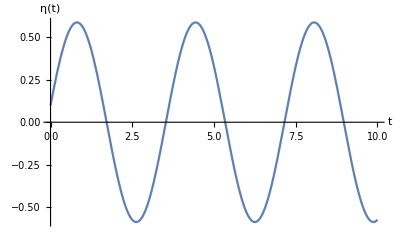

```mathematica
Plot[ Evaluate[ q[[1]] /. solution[t] ] , { t, 0, 10 } , AxesLabel-> { t , q[[1]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax }  , AxesLabel-> { q[[1]] , D[q[[1]], t] } , PlotRange-> 1.2 ]  ,
{ tmax , 1 ,20 , 0.5  } ]
```

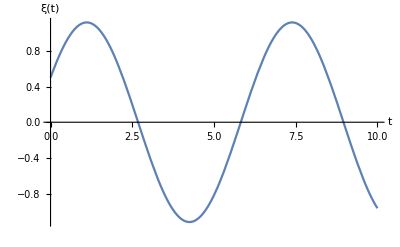

```mathematica
Plot[ Evaluate[ q[[2]] /. solution[t] ] , { t, 0, 10 } , AxesLabel-> { t , q[[2]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax }  , AxesLabel-> { q[[2]] , D[q[[2]], t] } , PlotRange-> 1.2 ]  ,
{ tmax , 1 ,20 , 0.5  } ]
```

```mathematica
D[q, t]
```

{η'[t],ξ'[t]}

```mathematica
Clear[𝓅]
𝓅 = 
Map[ p , q ]
```

{p[η[t]],p[ξ[t]]}

```mathematica
D[ ℒ , D[q[[1]], t] ] == 𝓅[[1]] 
D[ ℒ , D[q[[2]], t] ] == 𝓅[[2]]
```

m η'[t]==p[η[t]]

m ξ'[t]==p[ξ[t]]

```mathematica
D[ ℒ , D[q[[1]], t] ]
```

m η'[t]

```mathematica
Clear[momenta]
momenta = 
Flatten[Solve[Table[D[ ℒ , D[q[[i]], t] ]  == 𝓅[[i]] , { i, 1, 2 } ]  , D[q, t] ]]
```

{η'[t]→p[η[t]]/m,ξ'[t]→p[ξ[t]]/m}

```mathematica
Clear[ℋ]
ℋ = 
( Sum[ 𝓅[[i]] D[q[[i]], t] , { i, 1, 2 } ] - ℒ )   /. momenta // Expand
```

p[η[t]]^2/(2 m)+p[ξ[t]]^2/(2 m)+1/2 C η[t]^2+1/2 K η[t]^2-1/2 C ξ[t]^2+1/2 K ξ[t]^2